# mot heuristics

P. Huft

Qualitative diagrams about how a distribution of atoms subject to radiation force behaves for various tuning of the force parameters (as derived semi-classically).
All units dimensionless.

```mathematica
Clear[Δ,δ,γ,β]
(*two-beam 1D MOT force. stationary atom*)
(*b=Bℏ/μBg ~ βx for small B, s=I/Is*)
Fexact=(γ s)/(1+(4(Δ- b)^2)/γ+s)-(γ s)/(1+(4(Δ+ b)^2)/γ+s)/.b->β x;
Fsmall=Series[Fexact,{x,0,2}]//Normal;
"F, in the linear regime"
Collect[Fsmall,x]
```

F, in the linear regime

(16 s x β γ^2 Δ)/((γ+s γ+4 Δ^2)^2)

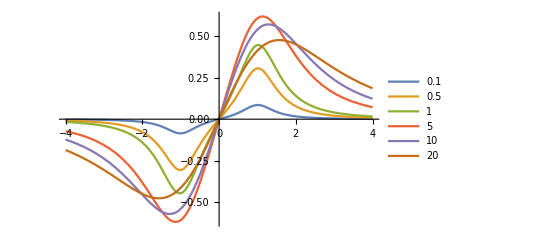

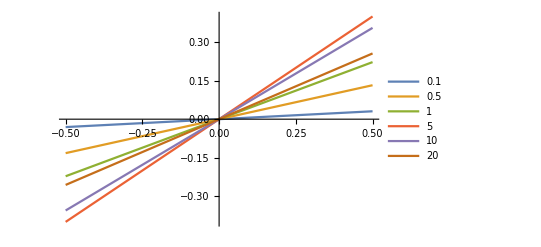

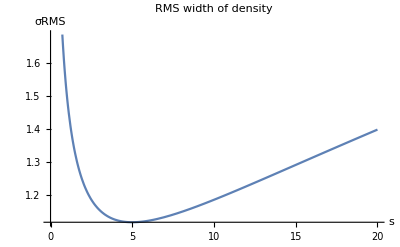

```mathematica
γ=Δ=1;
xmax =4;
β=1;
srange = {0.1,0.5,1,5,10,20};
Plot[Evaluate[Table[Fexact,{s,srange}]],{x,-xmax,xmax},PlotLegends->srange]
xmax =0.5;
β=1;
srange = {0.1,0.5,1,5,10,20};
Plot[Evaluate[Table[Fsmall,{s,srange}]],{x,-xmax,xmax},PlotLegends->srange]
Plot[(1/(Fsmall/x))^(1/2),{s,0,srange[[-1]]},PlotLabel->"RMS width of density",AxesLabel->{"s","σRMS"}]
```

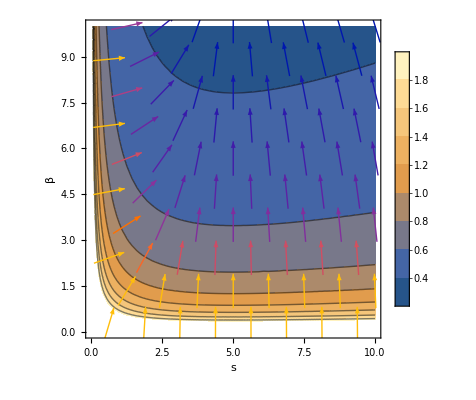

```mathematica
Clear[β];
γ=Δ=1;
σrms = 1/(Fsmall/x)^(1/2);
gradσ=-Grad[σrms,{s,β}];(*points toward smaller σrms*)
Show[ContourPlot[σrms,{s,0,10},{β,0,10},FrameLabel->{"s","β"},PlotLegends->Automatic],VectorPlot[gradσ,{s,0,20},{β,0,20}]]
```